```mathematica
Clear["Global`*"]
```

```mathematica
metaFile = FileNameJoin[{NotebookDirectory[],"output/gpu/meta.dat"}];
TcpuFile = FileNameJoin[{NotebookDirectory[],"output/cpu/T.dat"}];
TgpuFile = FileNameJoin[{NotebookDirectory[],"output/gpu/T.dat"}];
qcpuFile = FileNameJoin[{NotebookDirectory[],"output/cpu/q.dat"}];
qgpuFile = FileNameJoin[{NotebookDirectory[],"output/gpu/q.dat"}];
xFile = FileNameJoin[{NotebookDirectory[],"output/gpu/x.dat"}];
```

```mathematica
Lt = BinaryRead[metaFile, "UnsignedInteger32"]
Lx = BinaryRead[metaFile, "UnsignedInteger32"]
Close[metaFile];
```

50

400

```mathematica
Tcpu = BinaryReadList[TcpuFile, "Real32"];
Tgpu = BinaryReadList[TgpuFile, "Real32"];
qcpu = BinaryReadList[qcpuFile, "Real32"];
qgpu = BinaryReadList[qgpuFile, "Real32"];
x = BinaryReadList[xFile, "Real32"];
```

```mathematica
Tcpu = ArrayReshape[Tcpu , {Lt, Lx}];
Tgpu = ArrayReshape[Tgpu , {Lt, Lx}];
qcpu = ArrayReshape[qcpu , {Lt, Lx}];
qgpu = ArrayReshape[qgpu , {Lt, Lx}];
```

```mathematica
(*T$cpu = {};
T$gpu = {};
q$cpu = {};
q$gpu = {};
For[n=1,n <Lt, n=n++,
AppendTo[T$cpu,Transpose[{x,Tcpu[[n]]}]];
AppendTo[T$gpu,Transpose[{x,Tgpu[[n]]}]];
AppendTo[q$cpu,Transpose[{x,qcpu[[n]]}]];
AppendTo[q$gpu,Transpose[{x,qgpu[[n]]}]];
]*)
```

```mathematica
Manipulate[ListPlot[{Transpose[{x,Tgpu[[n]]}],Transpose[{x,qgpu[[n]]}]}, ImageSize->Large,Joined->True,PlotRange->Full],{n,1,Lt,1}]
```

```mathematica
Manipulate[ListPlot[{Transpose[{x,Tcpu[[n]]}],Transpose[{x,qcpu[[n]]}]}, ImageSize->Large,Joined->True,PlotRange->Full],{n,1,Lt,1}]
```

```mathematica
Manipulate[ListPlot[{Transpose[{x,Tcpu[[n]]}],Transpose[{x,Tgpu[[n]]}]}, ImageSize->Large, Joined->True, PlotRange->Full],{n,1,Lt,1}]
```

```mathematica
Manipulate[ListPlot[Transpose[{x,Tgpu[[n]] - Tcpu[[n]]}], ImageSize->Large],{n,1,Lt,1}]
```

```mathematica
Max[Tgpu - Tcpu]
```

Indeterminate

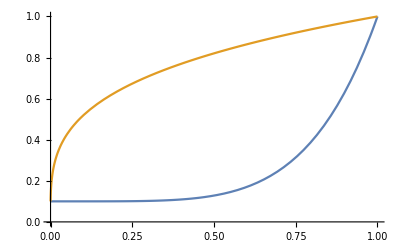

```mathematica
Plot[{0.1 + 0.9 x^5,(0.1^3.5+(1-0.1^3.5)x)^(2/7)},{x,0,1}]
```

```mathematica
vals = {fCFL-> 0.8, Δx->0.005}
```

{fCFL→0.8,Δx→0.005}

```mathematica
Δtdiff =fCFL 1/2 Δx^2 /. vals
```

0.00001

```mathematica
Δt = 50 Δtdiff
```

0.0005

```mathematica
τ = Δt^2/(fCFL Δx)^2/. vals
```

0.015625

```mathematica
τ/Δt
```

31.25

```mathematica
1/Δx/. vals
```

200.

```mathematica
T$cpu = {};
For[n=1,n <Lt, n=n+25,AppendTo[T$cpu,Transpose[{x,Tcpu[[n]]}]]]
ListPlot[Ttcpu,Joined->True]
```

ListPlot::lpn: Ttcpu is not a list of numbers or pairs of numbers.

ListPlot[Ttcpu,Joined→True]

```mathematica
1/400^2 //N
```

6.25×10^-6